```mathematica
inputFile = "problem3.txt";
outputFile = "W_out_NonEff.txt";

hull = {};
SetDirectory["/Users/pinev/Desktop/practice/st"];
pairs = ReadList[inputFile, Real];
pairs = Delete[pairs,1];
pairs=Partition[pairs,2];
amtOfPoint = Length[pairs]
```

100000

```mathematica
LineL[p1_, p2_, p_] := (p[[1]]-p1[[1]])*(p2[[2]]-p1[[2]])-(p[[2]]-p1[[2]])*(p2[[1]]-p1[[1]]);
```

```mathematica
DetSide[p1_,p2_,p_]:=Module[{res,Side},

res:=LineL[p1, p2, p];
If[res<0, Side = 1, If[res > 0, Side = -1, 0]]; 

Side
]
```

```mathematica
NoneEff[P_List] := Module[{it, maxX, pMaxX,prevPoint,nextPoint,SameSide, side, iterator, currPointSide},

If[amtOfPoint<3,Print["It's not possible to convex hull, n < 3";Abort]];

For[it= 2;maxX=1, it≤ amtOfPoint, it+=1,
If[pairs⟦it,1⟧>pairs⟦maxX,1⟧,maxX=it;maxX]];

pMaxX=pairs[[maxX]];
pairs=Delete[pairs,maxX];
PrependTo[pairs,pMaxX];
AppendTo[hull,pMaxX];
prevPoint=hull[[Length[hull]]];

For[it=2,it≤ Length[pairs],++it, 
nextPoint=pairs[[it]];
SameSide=True;
iterator=1;
side=0;

For[iterator=1,iterator≤ Length[pairs], ++iterator,

If[side≠ 0,++iterator;Break[];];
side=DetSide[prevPoint,nextPoint,pairs[[iterator]]];

];
For[Null,iterator≤ Length[pairs], ++iterator, currPointSide=DetSide[prevPoint,nextPoint,pairs[[iterator]]];

If[((currPointSide≠side)&&(currPointSide≠0)),
SameSide=False;Break[]]

];

If[((SameSide)&& !(MemberQ[hull,nextPoint])),AppendTo[hull,nextPoint];

prevPoint=nextPoint;
it=0]

];

str =StringReplace[ToString[SetPrecision[hull,17]] ,{ "{"->"", "}, "->"\n", ","->"", "}}" ->""}];
     str=StringJoin[{ToString[Length[hull]], "\n",str}];
     Export[outputFile, str];

gHull=hull;
AppendTo[gHull,hull[[1]]];
Graphics[{Point@P, Line@gHull}]

]
```

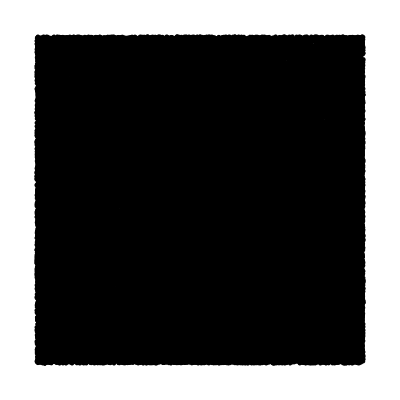
{98.3438,-Graphics-}

```mathematica
Timing[NoneEff[pairs]]
```

```mathematica
NoneEff[pairs]
```

-Graphics-

```mathematica
hull
```

{{100000.,-24118.8},{100000.,59453.1},{100000.,-24741.4},{100000.,-95178.1},{100000.,24369.},{100000.,-24118.8}}

```mathematica
Length[hull]
```

6

```mathematica
gHull
```

{{100000.,-24118.8},{100000.,59453.1},{100000.,-24741.4},{100000.,-95178.1},{100000.,24369.},{100000.,-24118.8},{100000.,-24118.8}}